# Predicting Climate Risks

## MGT529- Data Science and Machine Learning II

Jeanne Fernandez, Dario Scalabrin

## Data Loading & Cleaning

### Data Loading

```mathematica
ds = Import["https://raw.githubusercontent.com/scalabrindario/predicting-climate-risks/main/data/dataset_sample.csv", "Dataset", "HeaderLines" -> 1];(*Import dataset sample*)
comp = Import["https://raw.githubusercontent.com/scalabrindario/predicting-climate-risks/main/data/company_information.csv", "Dataset", "HeaderLines" -> 1];(*Import company information*)
```

### Data Cleaning

```mathematica
ds = KeyDrop[{""}]@ds; (*Drop emtpy column*)
ds = KeyDrop[{"Activity Description"}]@ds; (*Drop activity column*)
ds = ds[All,KeyMap[Replace[{"Ultimate Parent Name"->"Company", "Ultimate Parent ISIN"->"ISIN","ExposureScore_Composite_ModerateHigh_2020" -> "Risk2020",
"ExposureScore_Composite_ModerateHigh_2030" -> "Risk2030","ExposureScore_Composite_ModerateHigh_2040" -> "Risk2040","ExposureScore_Composite_ModerateHigh_2050" -> "Risk2050","ExposureScore_Composite_ModerateHigh_2060" ->"Risk2060",
"ExposureScore_Composite_ModerateHigh_2070" -> "Risk2070","ExposureScore_Composite_ModerateHigh_2080" -> "Risk2080",
"ExposureScore_Composite_ModerateHigh_2090"-> "Risk2090"}]]];(*Rename columns name*)
RandomSample[ds, 5]
comp = KeyDrop[{""}]@comp; (*Drop emtpy column*)
RandomSample[comp, 5]
```

## Feature Engineering

### Integral Score

Our goal it to give a summary of the risk approximation by decade into one scalar statistic, called Integral Score. 
We first visualise several options for this score, given the risk values by decade.
One can fit a function given the risk approximation for several years, and then integrate the resulting curve.
The choice of score then boils down to the choice of approximation.

{68,72,74,76,80,84,81,84}

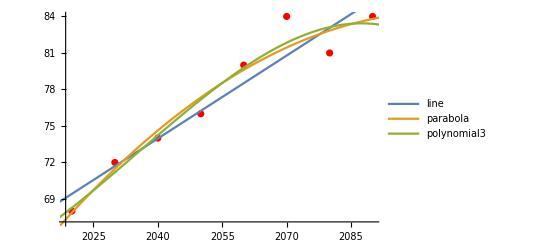

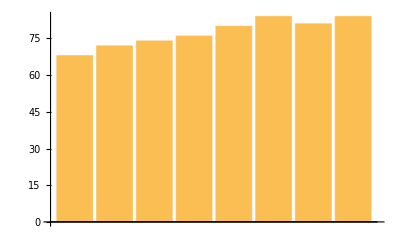

Linear approximation (line): 6280.95

Quardatic approximation (parabola): 6275.08

Third degree approximation (polynomial3): 6264.47

Rectangle approximation (barchart): 6190

```mathematica
x = {2020, 2030, 2040,2050,2060,2070, 2080, 2090};
yRandom = Normal@Values@RandomSample[ds[All, {6;;13}],1][[1,1]] (*We pick one row at random to illustrate all the possible scores*)
data = Transpose@Normal@{x,yRandom};
line = Fit[data, {1,z}, z];
parabola = Fit[data, {1,z,z^2}, z];
polynomial3 = Fit[data, {1,z,z^2,z^3}, z];
Show[ListPlot[data,PlotStyle->Red],Plot[{line, parabola, polynomial3},{z,2010,2100}, PlotLegends->"Expressions"]]
BarChart[yRandom]
Print["Linear approximation (line): ", Integrate[line,{z,2020,2100}]]
Print["Quardatic approximation (parabola): ",Integrate[parabola,{z,2020,2100}]]
Print["Third degree approximation (polynomial3): ",Integrate[polynomial3,{z,2020,2100}]]
Print["Rectangle approximation (barchart): ",(Total@yRandom)*10]
```

We note that all the approximations are in the same order of magnitude. For the sake of simplicity and to avoid overfitting, we choose the linear approximation. We add the chosen Integral Score to the dataset.

```mathematica
intColumn =ds[All,<|"integralScore"->Integrate[
Fit[Transpose@Normal@{x,{#Risk2020,#Risk2030,#Risk2040,#Risk2050,#Risk2060,#Risk2070,#Risk2080,#Risk2090}}, {1,z}, z]
,{z,2020,2100}]|>&];
newds=Join[ds,intColumn,2];
RandomSample[newds, 5]
```

### Computing Average of Integral Score

```mathematica
avgds= newds[GroupBy[{#Company}&]/*Values,<|"Company"->Query[First,"Company"],"ISIN"->Query[First,"ISIN"],"integralScore"->Query[Mean,"integralScore"]|>] ;(*Grouped and computed operations on some columns*)
RandomSample[avgds, 5]
```

### Merge the two datasets

```mathematica
merged = JoinAcross[avgds,comp,Key["ISIN"]];(*Merged two datasets and dropped rows without ISIN value*)
RandomSample[merged,5]
```

### Create Ratings

```mathematica
MinMaxScaler[value_]:=Rescale[value,{Min[merged[All, "integralScore"]],Max[merged[All, "integralScore"]]}];
MinMaxScaledList = Map[MinMaxScaler, merged[All, "integralScore"]];
RatingCreator[value_]:= 
If[Between[value,{0,0.2}], "A", 
If[Between[value,{0.2,0.4}], "B", 
If[Between[value,{0.4,0.6}], "C",
If[Between[value,{0.6,0.8}], "D",
If[Between[value,{0.8,1}], "E",   
]]]]]; (*Convert a numerical variable into a category*)
RatingsList = Map[RatingCreator, MinMaxScaledList];
IntScaledDat=Dataset[<|"IntScaled"->#|>&/@Normal[MinMaxScaledList]]; (*Convert the list into a dataset*)
RatingsDat=Dataset[<|"Ratings"->#|>&/@Normal[RatingsList]];(*Convert the list into a dataset*)
finalds = Join[merged,IntScaledDat,2]; (*Add Scaled Integral column to the dataset*)
finalds = Join[finalds,RatingsDat,2];(*Add Rating column to the dataset*)
RandomSample[finalds, 5]
```

### Add to the dataset the Total Carbon Intensity

```mathematica
CI1L = Normal[finalds[All, "Carbon Intensity-Scope 1 (tonnes CO2e/USD mn)"]];
CI2L = Normal[finalds[All,  "Carbon Intensity-Scope 2 (tonnes CO2e/USD mn)"]];
CI3L = Normal[finalds[All,  "Carbon Intensity-Scope 3 (tonnes CO2e/USD mn)"]];
CItotDat=Dataset[<|"Carbon Intensity Total (tonnes CO2e/USD mn)"->#|>&/@Normal[Total[{CI1L, CI2L, CI3L}]]]; (*Convert the list into a dataset*)
finalds = Join[finalds,CItotDat,2]; (*Add Carbon Intensity-Scope Total column to the dataset*)
RandomSample[finalds,5]
```

## Exploratory Data Analysis

```mathematica
Dimensions@finalds
```

{94,16}

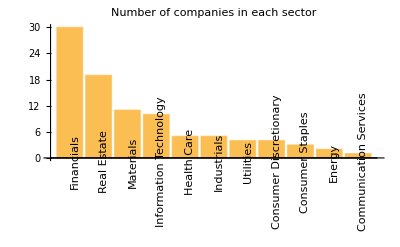

```mathematica
x1 = ReverseSort@Counts[finalds[All, "GICS Sector Name"]];
BarChart[x1,ChartLabels ->Placed[Normal@Keys@x1,Below, Rotate[#, Pi/2] &],PlotLabel->"Number of companies in each sector"]
```

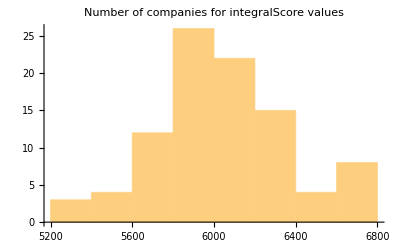

```mathematica
Histogram[finalds[All, "integralScore"],PlotLabel->"Number of companies for integralScore values"]
```

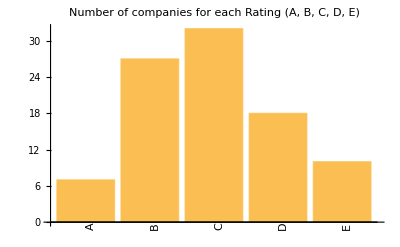

```mathematica
x2 = Counts[finalds[All, "Ratings"]];
x3 = {x2["A"], x2["B"], x2["C"], x2["D"], x2["E"]};
BarChart[x3,ChartLabels ->Placed[{"A","B","C","D","E"},Below, Rotate[#, Pi/2] &],PlotLabel->"Number of companies for each Rating (A, B, C, D, E) "]
```

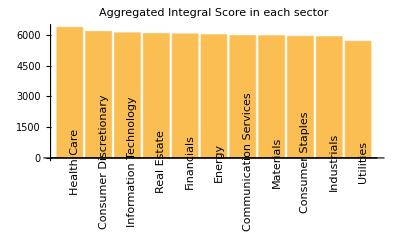

```mathematica
x4 = ReverseSort@finalds3[GroupBy["GICS Sector Name"],Mean,{"integralScore"}];
x5 = Flatten@Values@Values@Normal@x4;
BarChart[x5,ChartLabels -> Placed[Normal@Keys@x4,Below, Rotate[#, Pi/2] &],PlotLabel->"Aggregated Integral Score in each sector"]
```

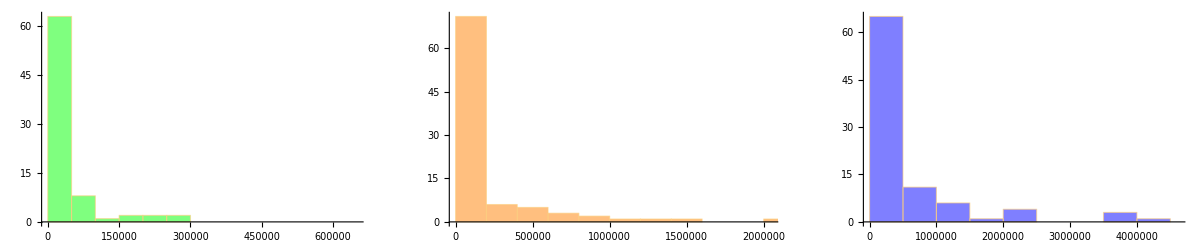

```mathematica
g1=Histogram[finalds[All, "Carbon-Scope 1  (tonnes CO2e)"],ChartStyle->{Directive[Green,Opacity[.5]]}];
g2=Histogram[finalds[All, "Carbon-Scope 2  (tonnes CO2e)"],ChartStyle->{Directive[Orange,Opacity[.5]]}];
g3=Histogram[finalds[All, "Carbon-Scope 3 (tonnes CO2e)"],ChartStyle->{Directive[Blue,Opacity[.5]]}];
GraphicsRow[{g1,g2, g3},PlotLabel->"Carbon-Scope 1,2,3 (tonnes CO2e)"]
```

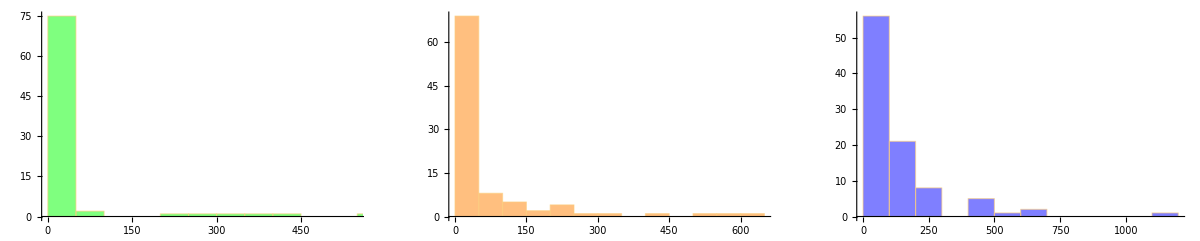

```mathematica
j1=Histogram[finalds[All, "Carbon Intensity-Scope 1 (tonnes CO2e/USD mn)"],ChartStyle->{Directive[Green,Opacity[.5]]}];
j2=Histogram[finalds[All, "Carbon Intensity-Scope 2 (tonnes CO2e/USD mn)"],ChartStyle->{Directive[Orange,Opacity[.5]]}];
j3=Histogram[finalds[All, "Carbon Intensity-Scope 3 (tonnes CO2e/USD mn)"],ChartStyle->{Directive[Blue,Opacity[.5]]}];
GraphicsRow[{j1,j2, j3},PlotLabel->"Carbon Intensity-Scope 1,2,3 (tonnes CO2e/USD mn)"]
```

```mathematica
Normal@Keys@First@finalds
```

{Company,ISIN,integralScore,TCUID,GICS Sector Name,Carbon-Scope 1  (tonnes CO2e),Carbon-Scope 2  (tonnes CO2e),Carbon-Scope 3 (tonnes CO2e),Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),IntScaled,Ratings,Carbon Intensity Total (tonnes CO2e/USD mn)}

```mathematica
revLog = Normal@finalds[All,"Revenue (USD mn)" ][Log];
scope1Log =  Normal@finalds[All,"Carbon-Scope 1  (tonnes CO2e)" ][Log];
scope2Log =  Normal@finalds[All,"Carbon-Scope 2  (tonnes CO2e)" ][Log];
scope3Log =  Normal@finalds[All,"Carbon-Scope 3 (tonnes CO2e)" ][Log];
scopeTotLog =  Normal@finalds[All,"Carbon Intensity Total (tonnes CO2e/USD mn)"][Log];
```

```mathematica
dataRev  =Dataset[<|"Log of Revenues (USD mn)"->Normal@revLog |>]//Transpose;
dataScope1Log  =Dataset[<|"Log of Scope 1 emissons (tonnes CO2e)"->Normal@scope1Log |>]//Transpose;
dataScope2Log  =Dataset[<|"Log of Scope 2 emissons (tonnes CO2e)"->Normal@scope2Log |>]//Transpose;
dataScope3Log  =Dataset[<|"Log of Scope 3 emissons (tonnes CO2e)"->Normal@scope3Log |>]//Transpose;
dataScopeTotLog  =Dataset[<|"Log of Carbon Intensity Total (tonnes CO2e/USD mn)"->Normal@scopeTotLog |>]//Transpose;
finalds2 = Join[finalds,dataRev ,2];
finalds3 = Join[finalds2,dataScope1Log ,2];
finalds4 = Join[finalds3,dataScope2Log ,2];
finalds5 = Join[finalds4,dataScope3Log ,2];
finalds6 = Join[finalds5,dataScopeTotLog ,2];
```

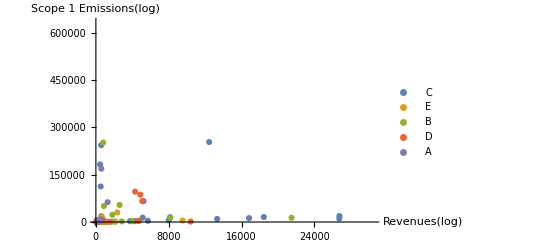

```mathematica
ListPlot[finalds3[GroupBy[Key["Ratings"]],All,{"Revenue (USD mn)","Carbon-Scope 1  (tonnes CO2e)"}], AxesLabel->{"Revenues(log)","Scope 1 Emissions(log)"}]
```

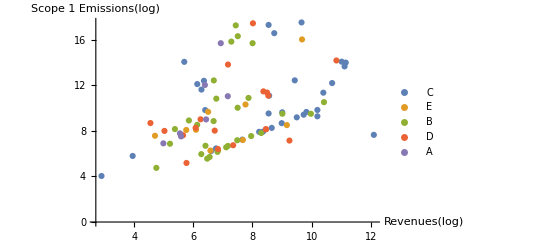

```mathematica
ListPlot[finalds3[GroupBy[Key["Ratings"]],All,{"Log of Revenues (USD mn)","Log of Scope 1 emissons (tonnes CO2e)"}], AxesLabel->{"Revenues(log)","Scope 1 Emissions(log)"}]
```

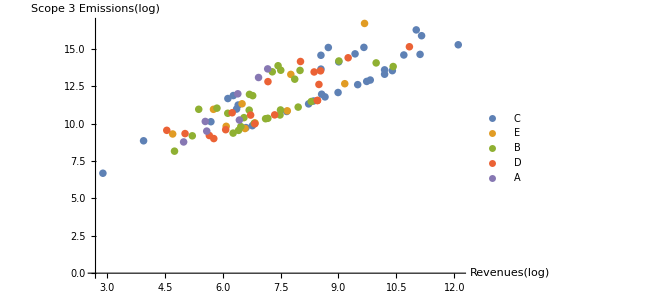

```mathematica
ListPlot[finalds5[GroupBy[Key["Ratings"]],All,{"Log of Revenues (USD mn)","Log of Scope 3 emissons (tonnes CO2e)"}], AxesLabel->{"Revenues(log)","Scope 3 Emissions(log)"}]
```

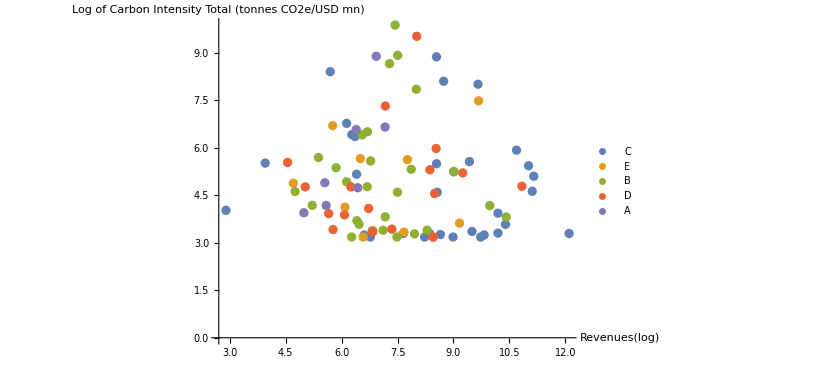

```mathematica
ListPlot[finalds6[GroupBy[Key["Ratings"]],All,{"Log of Revenues (USD mn)","Log of Carbon Intensity Total (tonnes CO2e/USD mn)"}], AxesLabel->{"Revenues(log)","Log of Carbon Intensity Total (tonnes CO2e/USD mn)"}]
```

```mathematica
ListPlot[finalds5[GroupBy[Key["Ratings"]],All,{ "integralScore", "Carbon-Scope 3 (tonnes CO2e)"}], AxesLabel->{"integral score","Scope 3 Emissions(log)"}]
```

-Graphics-

### Clustering

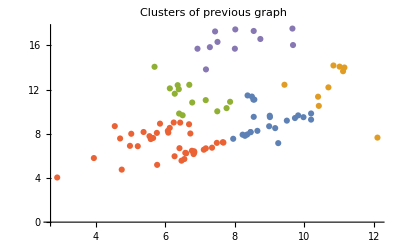

```mathematica
ListPlot[FindClusters[Transpose@Normal@{rev,disclosure}], PlotLabel->"Clusters"]
```

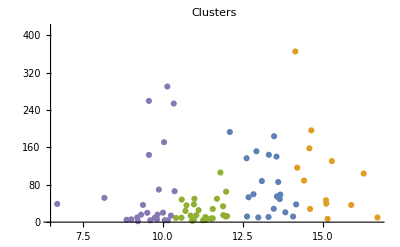

```mathematica
ListPlot[FindClusters[Transpose@Normal@{finalds5[All, "Log of Scope 3 emissons (tonnes CO2e)"], finalds5[All, "elevation"]}, nClusters], PlotLabel->"Clusters"]
```

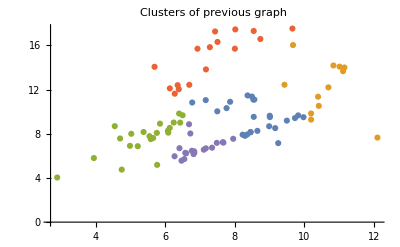

```mathematica
nClusters = 5;
ListPlot[FindClusters[Transpose@Normal@{rev,disclosure}, nClusters], PlotLabel->"Clusters"]
```

## Machine Learning

### Dataset Preparation

Prepare the dataset to use as an input for the machine learning models that we are going to create. In particular, we are going to divide the dataset in two new dataset: Training set, which includes 80% of all the rows of the dataset, while the Test set, which includes the remaining 20%.
The training set will be used to train our models, while the test set in order to understand the accuracy of our models.

```mathematica
datasetML = KeyDrop[{"Company", "ISIN", "TCUID", "integralScore", "IntScaled","Carbon-Scope 1  (tonnes CO2e)", "Carbon-Scope 2  (tonnes CO2e)", "Carbon-Scope 3 (tonnes CO2e)", "Carbon Intensity Total (tonnes CO2e/USD mn)"}]@finalds; (*Drop columns that are not needed for machine learning techniques*)
{nobs,ncol}=Dimensions[datasetML];(*Retrieve the number of rows and columns of the dataset*)
{trainingset,testset}=TakeDrop[RandomSample[datasetML],Round[nobs*0.8,1]];(*Divide the dataset in training set and test set*)
AccuracyAss = Association[];(*Create an empty association, to fill in with accuracy of our models*)
```

### Classification

#### Logistic Regression

Train a classifier using probabilities from linear combinations of features

```mathematica
cRisk = Classify[trainingset->"Ratings",Method->"LogisticRegression"]
Information[cRisk]
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 6)
Classes | ,,ABCDE
Accuracy | (45.15.) %
Method | LogisticRegression
Single evaluation time | 5.79 ms/example
Batch evaluation speed | 14. examples/ms
Loss | 1.47 ± 0.1
Model memory | 333. kB
Training examples used | 75 examples
Training time | 5.53 s
 |

The accuracy is: 0.315789

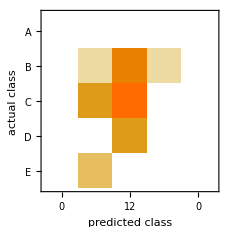

```mathematica
cm =ClassifierMeasurements[cRisk,testset]; (*Test our classifier on the test set*)
Print["The accuracy is: ",cm["Accuracy"] ](*Plot the accuracy of our model*)
AccuracyAss = Append[AccuracyAss, "LogisticRegression"->cm["Accuracy"]];
cm["ConfusionMatrixPlot"] (*Plot the Confusion Matrix*)
```

#### Gradient Boosted Trees

Train a classifier using an ensemble of trees trained with gradient boosting

```mathematica
cRisk = Classify[trainingset->"Ratings",Method->"GradientBoostedTrees"]
Information[cRisk]
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 6)
Classes | ,,ABCDE
Accuracy | (33.17.) %
Method | GradientBoostedTrees
Single evaluation time | 16.6 ms/example
Batch evaluation speed | 2.93 examples/ms
Loss | 1.56 ± 0.15
Model memory | 370. kB
Training examples used | 75 examples
Training time | 4.1 s
 |

The accuracy is: 0.473684

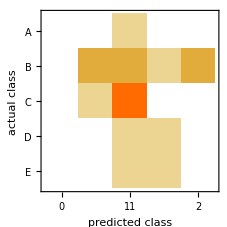

```mathematica
cm =ClassifierMeasurements[cRisk,testset]; (*Test our classifier on the test set*)
Print["The accuracy is: ",cm["Accuracy"] ](*Plot the accuracy of our model*)
AccuracyAss = Append[AccuracyAss, "GradientBoostedTrees"->cm["Accuracy"]];
cm["ConfusionMatrixPlot"] (*Plot the Confusion Matrix*)
```

#### RandomForest

Train a classifier using Breiman–Cutler ensembles of decision trees

```mathematica
cRisk = Classify[trainingset->"Ratings",Method->"RandomForest"]
Information[cRisk]
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 7)
Classes | ,,ABCDE
Accuracy | (35.5.) %
Method | RandomForest
Single evaluation time | 3.07 ms/example
Batch evaluation speed | 31.8 examples/ms
Loss | 1.56 ± 0.015
Model memory | 364. kB
Training examples used | 75 examples
Training time | 521. ms
 |

The accuracy is: 0.421053

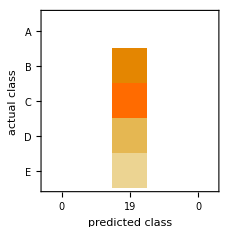

```mathematica
cm =ClassifierMeasurements[cRisk,testset]; (*Test our classifier on the test set*)
Print["The accuracy is: ",cm["Accuracy"] ](*Plot the accuracy of our model*)
AccuracyAss = Append[AccuracyAss, "RandomForest"->cm["Accuracy"]];
cm["ConfusionMatrixPlot"] (*Plot the Confusion Matrix*)
```

#### SupportVectorMachine

Train a classifier using a support vector machine

```mathematica
cRisk = Classify[trainingset->"Ratings",Method->"SupportVectorMachine"]
Information[cRisk]
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 6)
Classes | ,,ABCDE
Accuracy | (33.17.) %
Method | SupportVectorMachine
Single evaluation time | 15. ms/example
Batch evaluation speed | 3.62 examples/ms
Loss | 1.67 ± 0.28
Model memory | 406. kB
Training examples used | 75 examples
Training time | 4.79 s
 |

The accuracy is: 0.368421

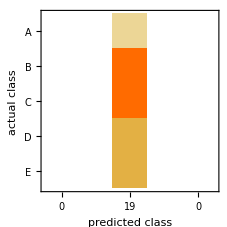

```mathematica
cm =ClassifierMeasurements[cRisk,testset]; (*Test our classifier on the test set*)
Print["The accuracy is: ",cm["Accuracy"] ](*Plot the accuracy of our model*)
AccuracyAss = Append[AccuracyAss, "SupportVectorMachine"->cm["Accuracy"]];
cm["ConfusionMatrixPlot"] (*Plot the Confusion Matrix*)
```

#### Nearest Neighbors

Train a classifier from nearest neighbor examples

```mathematica
cRisk = Classify[trainingset->"Ratings",Method->"NearestNeighbors"]
Information[cRisk]
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 7)
Classes | ,,ABCDE
Accuracy | (33.7.) %
Method | NearestNeighbors
Single evaluation time | 2.03 ms/example
Batch evaluation speed | 44.6 examples/ms
Loss | 1.5 ± 0.064
Model memory | 289. kB
Training examples used | 75 examples
Training time | 169. ms
 |

```mathematica
cm =ClassifierMeasurements[cRisk,testset]; (*Test our classifier on the test set*)
Print["The accuracy is: ",cm["Accuracy"] ](*Plot the accuracy of our model*)
AccuracyAss = Append[AccuracyAss, "NearestNeighbors"->cm["Accuracy"]];
cm["ConfusionMatrixPlot"] (*Plot the Confusion Matrix*)
```

The accuracy is: 0.421053

-Graphics-

### Neural Network

#### Encoding Data

Categorical variables cannot be used directly in neural networks and must be encoded as arrays.
Therefore, we create “Class” encoders that encode the categorical variables as one-hot encoded vectors

```mathematica
sectorEncoder=NetEncoder[{"Class",DeleteDuplicates[Normal[datasetML[All,"GICS Sector Name"]]],"UnitVector"}]
disclosureEncoder=NetEncoder[{"Class",DeleteDuplicates[Normal[datasetML[All, "Carbon Disclosure"]]],"UnitVector"}]
```

NetEncoder[<>]

NetEncoder[<>]

Applying the encoders to class labels produces unit vectors

```mathematica
sectorEncoder/@DeleteDuplicates[Normal[trainingset[All,"GICS Sector Name"]]];
disclosureEncoder/@DeleteDuplicates[Normal[trainingset[All,"Carbon Disclosure"]]];
```

Applying the Decoder to class labels that we want to predict

```mathematica
ratingsDecoder = NetDecoder[{"Class",DeleteDuplicates[Normal[datasetML[All, "Ratings"]]] }];
```

#### Create a Network

Create a network with an input corresponding to each feature and using a “Categorize” decoder to interpret the output of the net
The input features are first concatenated together before being further processed.

```mathematica
net=NetGraph[{CatenateLayer[],LinearLayer[],LogisticSigmoid},
{{NetPort["GICS Sector Name"],NetPort["Carbon Intensity-Scope 1 (tonnes CO2e/USD mn)"],NetPort["Carbon Intensity-Scope 2 (tonnes CO2e/USD mn)"],NetPort["Carbon Intensity-Scope 3 (tonnes CO2e/USD mn)"],NetPort["Carbon Disclosure"],NetPort["Revenue (USD mn)"]}->1,1->2->3->NetPort["Ratings"]},
"GICS Sector Name"->sectorEncoder,"Carbon Intensity-Scope 1 (tonnes CO2e/USD mn)"->"Scalar","Carbon Intensity-Scope 2 (tonnes CO2e/USD mn)"->"Scalar","Carbon Intensity-Scope 3 (tonnes CO2e/USD mn)"->"Scalar","Carbon Disclosure"->disclosureEncoder,"Revenue (USD mn)"->"Scalar","Ratings"->ratingsDecoder]
```

NetGraph[<>]

#### Training the Net

Train the net on the training data. NetTrain will automatically attach a Cross Entropy Loss layer to the output of the net
We set up two parameters:
- “Max Training Rounds”: is an option that specifies how many times to traverse the training data
- “Learning Rate”: is an option that specifies the rate at which to adjust neural net weights in order to minimize the training loss.

```mathematica
results=NetTrain[net,trainingset,All,MaxTrainingRounds->1000, LearningRate->0.01];
NetTrained=results["TrainedNet"]
```

NetGraph[<>]

#### Testing the Trained Neural Network

Plot the accuracy of the Neural Network on the Test Set

```mathematica
Print["The accuracy is: ",NetMeasurements[NetTrained,testset,"Accuracy"]]
AccuracyAss = Append[AccuracyAss, "NeuralNetwork"->NetMeasurements[NetTrained,testset,"Accuracy"]];
```

The accuracy is: 0.715789

### Comparing Accuracies

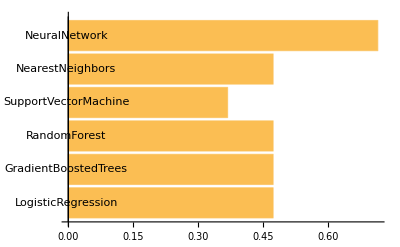

```mathematica
BarChart[AccuracyAss, ChartLabels->Keys[AccuracyAss], BarOrigin->Left]
```